## Dipole v2, full |J|^2, GlobalAdaptive

```mathematica
Quit[];
```

### J2Fun

```mathematica
ClearAll[dir];
dir=FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/hong/Dipole_v2_20230201/Int

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### Code: DipoleV2bN

```mathematica
ClearAll[DipoleV2b];
DipoleV2b=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{avg,avg2θk,precisiongoal,accuracygoal},

precisiongoal=6;
accuracygoal=6;

avg=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

avg2θk=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]Cos[2θk],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

avg2θk/avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleV2bN];
DipoleV2bN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleV2b[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### Code: DipoleSigmaN

```mathematica
ClearAll[DipoleSigma];
DipoleSigma=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{avg,avg2θk,precisiongoal,accuracygoal},

precisiongoal=6;
accuracygoal=6;

avg=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

(*avg2θk=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]Cos[2θk],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];*)

avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleSigmaN];
DipoleSigmaN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleSigma[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### test 1

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=0.1;
rAθ=0;
rB=0.1;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

96.244493

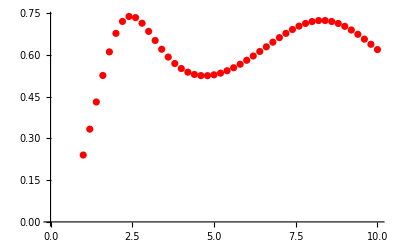

```mathematica
ListPlot[temp1,PlotStyle->Red]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

49.0466562

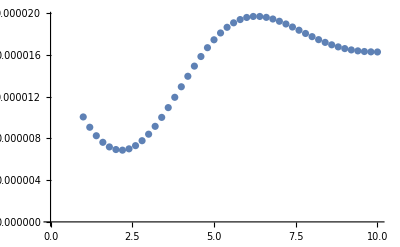

```mathematica
ListPlot[temp2]
```

### test 2

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=1;
rAθ=0;
rB=1;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

77.9518399

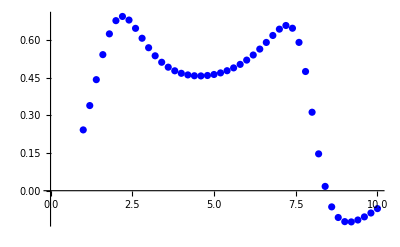

```mathematica
ListPlot[temp1,PlotStyle->Blue]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

28.342785

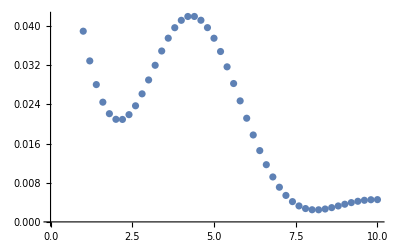

```mathematica
ListPlot[temp2]
```

### test 3

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=2;
rAθ=0;
rB=2;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

98.2155183

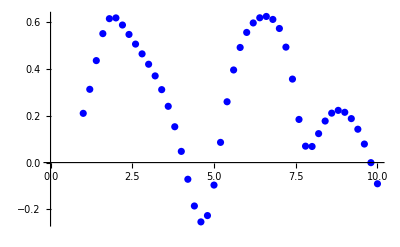

```mathematica
ListPlot[temp1,PlotStyle->Blue]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

28.269159

```mathematica
ListPlot[temp2]
```

-Graphics-

## b dependence for r_dp=1

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0.2;
by=0;
rA=1.0;
rAθ=π/2;
rB=1.0;
rBθ=π/2(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
ClearAll[ti,b02];
ti=AbsoluteTime[];
b02=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,30,0.2}]//Quiet;
AbsoluteTime[]-ti
$Aborted
8.714294`7.391777201428024
```

352.3954

$Aborted

8.714294

```mathematica
b02
```

{{1.,0.0199274},{1.2,0.029148},{1.4,0.0403887},{1.6,0.0538136},{1.8,0.0696026},{2.,0.0879378},{2.2,0.108978},{2.4,0.132813},{2.6,0.159386},{2.8,0.188368},{3.,0.218953},{3.2,0.249561},{3.4,0.277446},{3.6,0.298265},{3.8,0.305854},{4.,0.29269},{4.2,0.251629},{4.4,0.179053},{4.6,0.0780684},{4.8,-0.0408611},{5.,-0.163272},{5.2,-0.276003},{5.4,-0.370823},{5.6,-0.444857},{5.8,-0.498973},{6.,-0.535832},{6.2,-0.558502},{6.4,-0.569742},{6.6,-0.571737},{6.8,-0.56607},{7.,-0.553792},{7.2,-0.535509},{7.4,-0.511468},{7.6,-0.48164},{7.8,-0.445787},{8.,-0.403555},{8.2,-0.354601},{8.4,-0.298788},{8.6,-0.236501},{8.8,-0.169078},{9.,-0.0993531},{9.2,-0.0320935},{9.4,0.0260026},{9.6,0.0673232},{9.8,0.085393},{10.,0.0773342},{10.2,0.0451945},{10.4,-0.00481918},{10.6,-0.0646856},{10.8,-0.126971},{11.,-0.186194},{11.2,-0.239061},{11.4,-0.284035},{11.6,-0.32074},{11.8,-0.349445},{12.,-0.370704},{12.2,-0.385143},{12.4,-0.393341},{12.6,-0.395776},{12.8,-0.392803},{13.,-0.384654},{13.2,-0.371445},{13.4,-0.353193},{13.6,-0.329836},{13.8,-0.301261},{14.,-0.267352},{14.2,-0.228048},{14.4,-0.183435},{14.6,-0.133873},{14.8,-0.0801554},{15.,-0.0236993},{15.2,0.033284},{15.4,0.0877037},{15.6,0.135703},{15.8,0.173069},{16.,0.19596},{16.2,0.201783},{16.4,0.189911},{16.6,0.161902},{16.8,0.121105},{17.,0.0718378},{17.2,0.0184904},{17.4,-0.0351397},{17.6,-0.0861711},{17.8,-0.132667},{18.,-0.173491},{18.2,-0.208101},{18.4,-0.236348},{18.6,-0.258313},{18.8,-0.274185},{19.,-0.284191},{19.2,-0.288535},{19.4,-0.287381},{19.6,-0.280837},{19.8,-0.268958},{20.,-0.251758},{20.2,-0.22924},{20.4,-0.201433},{20.6,-0.168461},{20.8,-0.130629},{21.,-0.088542},{21.2,-0.0432536},{21.4,0.00358343},{21.6,0.0496009},{21.8,0.091707},{22.,0.126278},{22.2,0.149611},{22.4,0.158609},{22.6,0.151524},{22.8,0.128464},{23.,0.0914338},{23.2,0.0438566},{23.4,-0.0101885},{23.6,-0.0667357},{23.8,-0.122463},{24.,-0.174923},{24.2,-0.222524},{24.4,-0.264386},{24.6,-0.300142},{24.8,-0.329758},{25.,-0.353388},{25.2,-0.37127},{25.4,-0.383657},{25.6,-0.390767},{25.8,-0.39277},{26.,-0.389767},{26.2,-0.381794},{26.4,-0.368837},{26.6,-0.350849},{26.8,-0.327798},{27.,-0.299735},{27.2,-0.266897},{27.4,-0.229864},{27.6,-0.189763},{27.8,-0.148497},{28.,-0.108942},{28.2,-0.0749767},{28.4,-0.0511611},{28.6,-0.0419412},{28.8,-0.0504749},{29.,-0.0775133},{29.2,-0.12097},{29.4,-0.176434},{29.6,-0.238458},{29.8,-0.301874},{30.,-0.362663}}

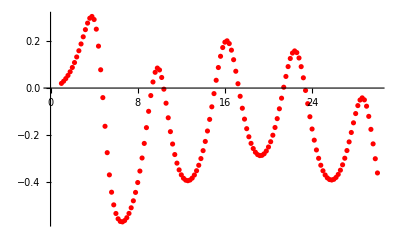

```mathematica
ListPlot[b02,PlotStyle->Red]
```

```mathematica
Getv2kT[b_]:=Module[{bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y,ti,b02},
bx=b;
by=0;
rA=1.0;
rAθ=π/2;
rB=1.0;
rBθ=π/2(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
ClearAll[ti,b02];
ti=AbsoluteTime[];
b02=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,0.2,30,0.2}]//Quiet;
Print["For b = ",b," Computation time: ",AbsoluteTime[]-ti];
Print[ListPlot[b02,PlotStyle->Red]];
b02
]
```

For b = 0.6 Computation time: 560.73188

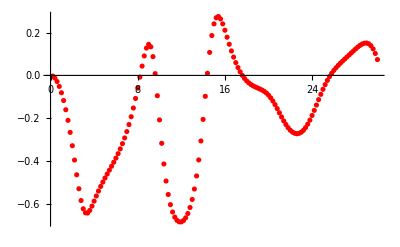

{{0.2,-0.00308956},{0.4,-0.0125312},{0.6,-0.0285733},{0.8,-0.0513548},{1.,-0.0808985},{1.2,-0.11716},{1.4,-0.160091},{1.6,-0.209659},{1.8,-0.265764},{2.,-0.32795},{2.2,-0.394857},{2.4,-0.463475},{2.6,-0.528636},{2.8,-0.58356},{3.,-0.621983},{3.2,-0.640923},{3.4,-0.641909},{3.6,-0.629676},{3.8,-0.609693},{4.,-0.586367},{4.2,-0.562492},{4.4,-0.539491},{4.6,-0.517869},{4.8,-0.497615},{5.,-0.478462},{5.2,-0.460037},{5.4,-0.441938},{5.6,-0.423763},{5.8,-0.405125},{6.,-0.385642},{6.2,-0.364939},{6.4,-0.342632},{6.6,-0.318325},{6.8,-0.291605},{7.,-0.26204},{7.2,-0.229194},{7.4,-0.192659},{7.6,-0.152119},{7.8,-0.107474},{8.,-0.0590556},{8.2,-0.00796415},{8.4,0.0434095},{8.6,0.0907826},{8.8,0.127495},{9.,0.144749},{9.2,0.133394},{9.4,0.0875138},{9.6,0.0083176},{9.8,-0.0948061},{10.,-0.207667},{10.2,-0.316766},{10.4,-0.413093},{10.6,-0.492722},{10.8,-0.555411},{11.,-0.602841},{11.2,-0.637317},{11.4,-0.661051},{11.6,-0.675841},{11.8,-0.682986},{12.,-0.683283},{12.2,-0.677057},{12.4,-0.664193},{12.6,-0.644157},{12.8,-0.616016},{13.,-0.578476},{13.2,-0.529991},{13.4,-0.468978},{13.6,-0.394253},{13.8,-0.305716},{14.,-0.205241},{14.2,-0.0975189},{14.4,0.0098161},{14.6,0.107295},{14.8,0.18603},{15.,0.240304},{15.2,0.268972},{15.4,0.27496},{15.6,0.263498},{15.8,0.240406},{16.,0.210651},{16.2,0.17809},{16.4,0.145363},{16.6,0.114133},{16.8,0.0853528},{17.,0.059483},{17.2,0.036693},{17.4,0.0169503},{17.6,0.000118996},{17.8,-0.0140091},{18.,-0.0256854},{18.2,-0.0351931},{18.4,-0.0428534},{18.6,-0.0490296},{18.8,-0.0541357},{19.,-0.0586465},{19.2,-0.0630955},{19.4,-0.06807},{19.6,-0.0741716},{19.8,-0.0819821},{20.,-0.091958},{20.2,-0.104377},{20.4,-0.119247},{20.6,-0.136284},{20.8,-0.154908},{21.,-0.174366},{21.2,-0.193782},{21.4,-0.21231},{21.6,-0.22919},{21.8,-0.243801},{22.,-0.255674},{22.2,-0.264469},{22.4,-0.269949},{22.6,-0.271942},{22.8,-0.27034},{23.,-0.265074},{23.2,-0.256132},{23.4,-0.243582},{23.6,-0.227621},{23.8,-0.208521},{24.,-0.186811},{24.2,-0.163129},{24.4,-0.13825},{24.6,-0.113033},{24.8,-0.0883113},{25.,-0.0647848},{25.2,-0.0430091},{25.4,-0.0232982},{25.6,-0.00571541},{25.8,0.00981294},{26.,0.0235291},{26.2,0.0357563},{26.4,0.0468379},{26.6,0.0571109},{26.8,0.0668933},{27.,0.0764165},{27.2,0.0858686},{27.4,0.0953541},{27.6,0.104885},{27.8,0.114382},{28.,0.123664},{28.2,0.132417},{28.4,0.140195},{28.6,0.146397},{28.8,0.150263},{29.,0.150912},{29.2,0.147351},{29.4,0.138577},{29.6,0.123713},{29.8,0.102177},{30.,0.0738465}}

```mathematica
Getv2kT[0.6]
```

```mathematica
|
```

For b = 0.7 Computation time: 703.043911

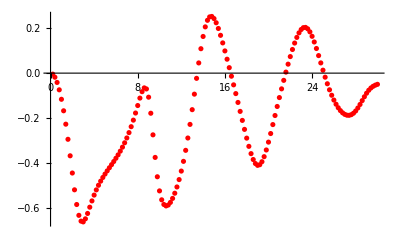

{{0.2,-0.00448635},{0.4,-0.0181794},{0.6,-0.041353},{0.8,-0.074045},{1.,-0.116059},{1.2,-0.167028},{1.4,-0.226441},{1.6,-0.293496},{1.8,-0.366692},{2.,-0.443099},{2.2,-0.517587},{2.4,-0.582793},{2.6,-0.630806},{2.8,-0.65645},{3.,-0.659895},{3.2,-0.646214},{3.4,-0.622423},{3.6,-0.594627},{3.8,-0.566813},{4.,-0.541002},{4.2,-0.517882},{4.4,-0.497414},{4.6,-0.479223},{4.8,-0.462824},{5.,-0.44773},{5.2,-0.43349},{5.4,-0.419705},{5.6,-0.406018},{5.8,-0.392111},{6.,-0.377683},{6.2,-0.362449},{6.4,-0.346123},{6.6,-0.328409},{6.8,-0.309004},{7.,-0.287591},{7.2,-0.263861},{7.4,-0.237552},{7.6,-0.208533},{7.8,-0.176987},{8.,-0.143736},{8.2,-0.110818},{8.4,-0.0823493},{8.6,-0.0654449},{8.8,-0.0701927},{9.,-0.10667},{9.2,-0.177939},{9.4,-0.273772},{9.6,-0.373886},{9.8,-0.459686},{10.,-0.52236},{10.2,-0.561938},{10.4,-0.582584},{10.6,-0.589034},{10.8,-0.585111},{11.,-0.573457},{11.2,-0.555705},{11.4,-0.532739},{11.6,-0.504918},{11.8,-0.472245},{12.,-0.434501},{12.2,-0.391359},{12.4,-0.342508},{12.6,-0.287802},{12.8,-0.227425},{13.,-0.162095},{13.2,-0.0932464},{13.4,-0.02315},{13.6,0.0452358},{13.8,0.108326},{14.,0.162617},{14.2,0.205196},{14.4,0.234263},{14.6,0.249372},{14.8,0.251362},{15.,0.241977},{15.2,0.223429},{15.4,0.19798},{15.6,0.167653},{15.8,0.13409},{16.,0.098506},{16.2,0.0617274},{16.4,0.0242475},{16.6,-0.0136928},{16.8,-0.0520257},{17.,-0.0907862},{17.2,-0.130025},{17.4,-0.169731},{17.6,-0.209723},{17.8,-0.24954},{18.,-0.288337},{18.2,-0.324795},{18.4,-0.35714},{18.6,-0.383265},{18.8,-0.401107},{19.,-0.409025},{19.2,-0.406212},{19.4,-0.392967},{19.6,-0.370546},{19.8,-0.340858},{20.,-0.306015},{20.2,-0.267974},{20.4,-0.228245},{20.6,-0.187989},{20.8,-0.147907},{21.,-0.10842},{21.2,-0.0697612},{21.4,-0.0320648},{21.6,0.00451659},{21.8,0.0397713},{22.,0.073368},{22.2,0.10481},{22.4,0.133424},{22.6,0.158373},{22.8,0.178698},{23.,0.193421},{23.2,0.201658},{23.4,0.202772},{23.6,0.19652},{23.8,0.183129},{24.,0.163317},{24.2,0.138216},{24.4,0.109209},{24.6,0.0777809},{24.8,0.0453357},{25.,0.0130926},{25.2,-0.0179727},{25.4,-0.04715},{25.6,-0.0739591},{25.8,-0.0981143},{26.,-0.119464},{26.2,-0.137941},{26.4,-0.153534},{26.6,-0.166247},{26.8,-0.176053},{27.,-0.18288},{27.2,-0.186622},{27.4,-0.187133},{27.6,-0.184237},{27.8,-0.177804},{28.,-0.167857},{28.2,-0.154679},{28.4,-0.138996},{28.6,-0.121891},{28.8,-0.104804},{29.,-0.0891342},{29.2,-0.0760185},{29.4,-0.0658528},{29.6,-0.0584959},{29.8,-0.053357},{30.,-0.0496783}}

```mathematica
Getv2kT[0.7]
```

For b = 0.8 Computation time: 698.713013

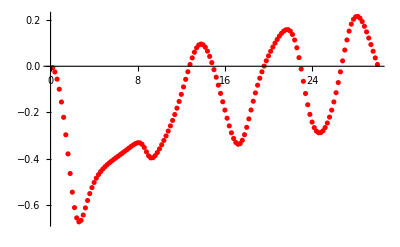

{{0.2,-0.00606924},{0.4,-0.0245709},{0.6,-0.0557477},{0.8,-0.0994044},{1.,-0.154921},{1.2,-0.2213},{1.4,-0.297046},{1.6,-0.379678},{1.8,-0.464868},{2.,-0.545625},{2.2,-0.612646},{2.4,-0.657025},{2.6,-0.674503},{2.8,-0.667817},{3.,-0.644747},{3.2,-0.613906},{3.4,-0.58175},{3.6,-0.551906},{3.8,-0.525835},{4.,-0.503737},{4.2,-0.485215},{4.4,-0.469684},{4.6,-0.456537},{4.8,-0.44524},{5.,-0.435349},{5.2,-0.426502},{5.4,-0.418414},{5.6,-0.410857},{5.8,-0.403653},{6.,-0.396658},{6.2,-0.389759},{6.4,-0.382866},{6.6,-0.375913},{6.8,-0.36886},{7.,-0.361702},{7.2,-0.35449},{7.4,-0.347375},{7.6,-0.340677},{7.8,-0.335017},{8.,-0.331497},{8.2,-0.331866},{8.4,-0.33831},{8.6,-0.352092},{8.8,-0.37093},{9.,-0.388146},{9.2,-0.397119},{9.4,-0.396103},{9.6,-0.387372},{9.8,-0.373924},{10.,-0.357842},{10.2,-0.340209},{10.4,-0.321455},{10.6,-0.301649},{10.8,-0.280691},{11.,-0.2584},{11.2,-0.234582},{11.4,-0.209063},{11.6,-0.181734},{11.8,-0.152593},{12.,-0.121748},{12.2,-0.0895694},{12.4,-0.0566448},{12.6,-0.0238548},{12.8,0.00762678},{13.,0.0363942},{13.2,0.0609346},{13.4,0.079807},{13.6,0.0918458},{13.8,0.0963433},{14.,0.0931397},{14.2,0.0826058},{14.4,0.0655147},{14.6,0.0429062},{14.8,0.0158782},{15.,-0.0145241},{15.2,-0.0473909},{15.4,-0.0819715},{15.6,-0.117638},{15.8,-0.153822},{16.,-0.189909},{16.2,-0.225123},{16.4,-0.258401},{16.6,-0.288292},{16.8,-0.312936},{17.,-0.330202},{17.2,-0.338039},{17.4,-0.335009},{17.6,-0.320817},{17.8,-0.296594},{18.,-0.264682},{18.2,-0.228049},{18.4,-0.189567},{18.6,-0.15154},{18.8,-0.115471},{19.,-0.0821325},{19.2,-0.0517424},{19.4,-0.0241667},{19.6,0.000908862},{19.8,0.0238563},{20.,0.0450425},{20.2,0.0647579},{20.4,0.0831971},{20.6,0.100427},{20.8,0.116359},{21.,0.130725},{21.2,0.143023},{21.4,0.152494},{21.6,0.158094},{21.8,0.158505},{22.,0.15221},{22.2,0.137704},{22.4,0.113804},{22.6,0.0801077},{22.8,0.0373949},{23.,-0.0121772},{23.2,-0.0652686},{23.4,-0.117992},{23.6,-0.16668},{23.8,-0.20852},{24.,-0.241847},{24.2,-0.266048},{24.4,-0.28128},{24.6,-0.288138},{24.8,-0.287364},{25.,-0.279678},{25.2,-0.265689},{25.4,-0.245863},{25.6,-0.220553},{25.8,-0.189978},{26.,-0.154496},{26.2,-0.114517},{26.4,-0.0707457},{26.6,-0.0242374},{26.8,0.0234697},{27.,0.0703664},{27.2,0.114112},{27.4,0.152251},{27.6,0.182602},{27.8,0.203624},{28.,0.214628},{28.2,0.215873},{28.4,0.208368},{28.6,0.19362},{28.8,0.173306},{29.,0.149047},{29.2,0.122266},{29.4,0.0940428},{29.6,0.0652011},{29.8,0.0362999},{30.,0.00768729}}

```mathematica
Getv2kT[0.8]
```

For b = 0.9 Computation time: 749.971517

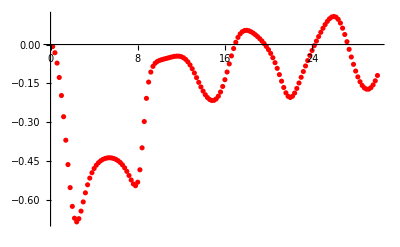

{{0.2,-0.00784224},{0.4,-0.0317149},{0.6,-0.0717477},{0.8,-0.127333},{1.,-0.197142},{1.2,-0.279092},{1.4,-0.369902},{1.6,-0.464137},{1.8,-0.553206},{2.,-0.625808},{2.2,-0.67143},{2.4,-0.685768},{2.6,-0.67329},{2.8,-0.644105},{3.,-0.608448},{3.2,-0.573342},{3.4,-0.54231},{3.6,-0.516473},{3.8,-0.495684},{4.,-0.479303},{4.2,-0.466581},{4.4,-0.456842},{4.6,-0.449532},{4.8,-0.444231},{5.,-0.440636},{5.2,-0.438548},{5.4,-0.437853},{5.6,-0.438512},{5.8,-0.440554},{6.,-0.444069},{6.2,-0.449207},{6.4,-0.456172},{6.6,-0.465208},{6.8,-0.476561},{7.,-0.490368},{7.2,-0.50644},{7.4,-0.523697},{7.6,-0.539113},{7.8,-0.545937},{8.,-0.532248},{8.2,-0.484225},{8.4,-0.399305},{8.6,-0.29765},{8.8,-0.208161},{9.,-0.145116},{9.2,-0.106454},{9.4,-0.0844584},{9.6,-0.0723055},{9.8,-0.0655021},{10.,-0.0614094},{10.2,-0.0585616},{10.4,-0.056217},{10.6,-0.053931},{10.8,-0.0516514},{11.,-0.0493962},{11.2,-0.0473185},{11.4,-0.0456714},{11.6,-0.0447905},{11.8,-0.0450875},{12.,-0.0470169},{12.2,-0.0510402},{12.4,-0.0575548},{12.6,-0.0668141},{12.8,-0.0788807},{13.,-0.0934893},{13.2,-0.110115},{13.4,-0.127992},{13.6,-0.14621},{13.8,-0.16383},{14.,-0.179979},{14.2,-0.193894},{14.4,-0.204947},{14.6,-0.212589},{14.8,-0.216334},{15.,-0.215712},{15.2,-0.210267},{15.4,-0.199612},{15.6,-0.183518},{15.8,-0.162081},{16.,-0.135905},{16.2,-0.106205},{16.4,-0.0747973},{16.6,-0.0438502},{16.8,-0.0154837},{17.,0.00863274},{17.2,0.0275691},{17.4,0.0411348},{17.6,0.049706},{17.8,0.0540113},{18.,0.0548801},{18.2,0.0531081},{18.4,0.0493562},{18.6,0.0441361},{18.8,0.037802},{19.,0.0305607},{19.2,0.0225027},{19.4,0.0135972},{19.6,0.00372388},{19.8,-0.00733852},{20.,-0.0198872},{20.2,-0.0342923},{20.4,-0.0509415},{20.6,-0.0701596},{20.8,-0.0920606},{21.,-0.116283},{21.2,-0.141671},{21.4,-0.166108},{21.6,-0.18663},{21.8,-0.200179},{22.,-0.204701},{22.2,-0.199975},{22.4,-0.18748},{22.6,-0.169599},{22.8,-0.148693},{23.,-0.126587},{23.2,-0.104436},{23.4,-0.0828511},{23.6,-0.0620705},{23.8,-0.0421262},{24.,-0.0229508},{24.2,-0.00445336},{24.4,0.0134165},{24.6,0.0306991},{24.8,0.047259},{25.,0.0628788},{25.2,0.0771883},{25.4,0.0896767},{25.6,0.0996582},{25.8,0.106235},{26.,0.108561},{26.2,0.105816},{26.4,0.0973945},{26.6,0.0831119},{26.8,0.0632915},{27.,0.038812},{27.2,0.011004},{27.4,-0.0185471},{27.6,-0.04823},{27.8,-0.0766094},{28.,-0.102535},{28.2,-0.125126},{28.4,-0.143789},{28.6,-0.15811},{28.8,-0.167784},{29.,-0.17258},{29.2,-0.172308},{29.4,-0.166815},{29.6,-0.156066},{29.8,-0.140202},{30.,-0.119643}}

```mathematica
Getv2kT[0.9]
```

For b = 1. Computation time: 796.887418

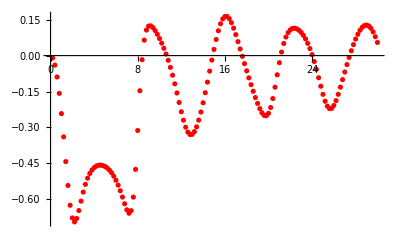

{{0.2,-0.00980839},{0.4,-0.0396154},{0.6,-0.0893263},{0.8,-0.157685},{1.,-0.242273},{1.2,-0.339263},{1.4,-0.442491},{1.6,-0.542167},{1.8,-0.62492},{2.,-0.677615},{2.2,-0.694282},{2.4,-0.679955},{2.6,-0.646913},{2.8,-0.607463},{3.,-0.569738},{3.2,-0.537527},{3.4,-0.511795},{3.6,-0.492163},{3.8,-0.477781},{4.,-0.467766},{4.2,-0.461373},{4.4,-0.458032},{4.6,-0.457349},{4.8,-0.45908},{5.,-0.463108},{5.2,-0.469425},{5.4,-0.478118},{5.6,-0.489354},{5.8,-0.503361},{6.,-0.520401},{6.2,-0.540699},{6.4,-0.564299},{6.6,-0.590759},{6.8,-0.618535},{7.,-0.643758},{7.2,-0.658262},{7.4,-0.647364},{7.6,-0.590927},{7.8,-0.474967},{8.,-0.3127},{8.2,-0.146816},{8.4,-0.0171377},{8.6,0.0644736},{8.8,0.106758},{9.,0.123171},{9.2,0.12428},{9.4,0.116716},{9.6,0.104284},{9.8,0.0888565},{10.,0.071309},{10.2,0.0518881},{10.4,0.0304748},{10.6,0.00675587},{10.8,-0.0196606},{11.,-0.0491431},{11.2,-0.081887},{11.4,-0.117769},{11.6,-0.156145},{11.8,-0.195729},{12.,-0.234489},{12.2,-0.269828},{12.4,-0.298942},{12.6,-0.319361},{12.8,-0.329456},{13.,-0.328691},{13.2,-0.317571},{13.4,-0.297315},{13.6,-0.269471},{13.8,-0.235591},{14.,-0.197058},{14.2,-0.155051},{14.4,-0.110625},{14.6,-0.0648288},{14.8,-0.0188643},{15.,0.0257865},{15.2,0.0673265},{15.4,0.103709},{15.6,0.132872},{15.8,0.153087},{16.,0.163312},{16.2,0.163429},{16.4,0.154266},{16.6,0.137317},{16.8,0.114467},{17.,0.0875722},{17.2,0.0582524},{17.4,0.0277599},{17.6,-0.00303874},{17.8,-0.03359},{18.,-0.0635916},{18.2,-0.0928928},{18.4,-0.121386},{18.6,-0.148933},{18.8,-0.17524},{19.,-0.199742},{19.2,-0.221454},{19.4,-0.238823},{19.6,-0.24965},{19.8,-0.251232},{20.,-0.240835},{20.2,-0.216719},{20.4,-0.179329},{20.6,-0.13194},{20.8,-0.0800615},{21.,-0.0296442},{21.2,0.0147009},{21.4,0.0505342},{21.6,0.0773824},{21.8,0.0959592},{22.,0.107506},{22.2,0.113291},{22.4,0.114402},{22.6,0.111656},{22.8,0.105584},{23.,0.0964826},{23.2,0.0844701},{23.4,0.0694071},{23.6,0.0511595},{23.8,0.0294651},{24.,0.00412},{24.2,-0.0249293},{24.4,-0.0573622},{24.6,-0.0922634},{24.8,-0.127916},{25.,-0.161741},{25.2,-0.19054},{25.4,-0.211149},{25.6,-0.221239},{25.8,-0.220002},{26.,-0.208227},{26.2,-0.187962},{26.4,-0.161663},{26.6,-0.131763},{26.8,-0.100213},{27.,-0.06843},{27.2,-0.037374},{27.4,-0.00767716},{27.6,0.0202107},{27.8,0.0459177},{28.,0.0690481},{28.2,0.0891482},{28.4,0.105684},{28.6,0.118006},{28.8,0.125478},{29.,0.127522},{29.2,0.123759},{29.4,0.114112},{29.6,0.0989052},{29.8,0.0788562},{30.,0.0550126}}

```mathematica
Getv2kT[1.0]
```

For b = 1.1 Computation time: 781.059734

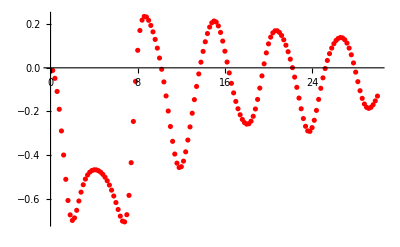

{{0.2,-0.0119689},{0.4,-0.0482718},{0.6,-0.108442},{0.8,-0.190273},{1.,-0.289748},{1.2,-0.400409},{1.4,-0.511881},{1.6,-0.609047},{1.8,-0.675255},{2.,-0.700673},{2.2,-0.688964},{2.4,-0.654184},{2.6,-0.611441},{2.8,-0.570824},{3.,-0.53691},{3.2,-0.510763},{3.4,-0.491835},{3.6,-0.479081},{3.8,-0.471473},{4.,-0.468182},{4.2,-0.468607},{4.4,-0.472363},{4.6,-0.479243},{4.8,-0.489185},{5.,-0.502246},{5.2,-0.518563},{5.4,-0.538315},{5.6,-0.561653},{5.8,-0.588561},{6.,-0.618609},{6.2,-0.650458},{6.4,-0.68098},{6.6,-0.703799},{6.8,-0.707404},{7.,-0.674343},{7.2,-0.585718},{7.4,-0.435472},{7.6,-0.246184},{7.8,-0.0621885},{8.,0.08043},{8.2,0.171423},{8.4,0.2189},{8.6,0.235867},{8.8,0.233194},{9.,0.218064},{9.2,0.194683},{9.4,0.165196},{9.6,0.13046},{9.8,0.0905311},{10.,0.0450215},{10.2,-0.00660139},{10.4,-0.0647021},{10.6,-0.129054},{10.8,-0.198308},{11.,-0.269452},{11.2,-0.337509},{11.4,-0.39588},{11.6,-0.437659},{11.8,-0.457614},{12.,-0.453885},{12.2,-0.428392},{12.4,-0.385783},{12.6,-0.331686},{12.8,-0.271262},{13.,-0.208477},{13.2,-0.146006},{13.4,-0.0854996},{13.6,-0.0279583},{13.8,0.0259148},{14.,0.0754275},{14.2,0.119676},{14.4,0.157427},{14.6,0.187097},{14.8,0.206872},{15.,0.215008},{15.2,0.210283},{15.4,0.192433},{15.6,0.162518},{15.8,0.122767},{16.,0.0763431},{16.2,0.026615},{16.4,-0.0233486},{16.6,-0.0711373},{16.8,-0.115088},{17.,-0.154167},{17.2,-0.187772},{17.4,-0.215491},{17.6,-0.236906},{17.8,-0.251478},{18.,-0.258369},{18.2,-0.256582},{18.4,-0.24496},{18.6,-0.222539},{18.8,-0.188961},{19.,-0.145034},{19.2,-0.0930991},{19.4,-0.0370249},{19.6,0.0184316},{19.8,0.0686361},{20.,0.110068},{20.2,0.140825},{20.4,0.160534},{20.6,0.169904},{20.8,0.170178},{21.,0.162685},{21.2,0.148548},{21.4,0.128749},{21.6,0.103818},{21.8,0.0740744},{22.,0.0396811},{22.2,0.000738406},{22.4,-0.0425588},{22.6,-0.0895456},{22.8,-0.138862},{23.,-0.187948},{23.2,-0.232878},{23.4,-0.268499},{23.6,-0.289431},{23.8,-0.291751},{24.,-0.274603},{24.2,-0.240755},{24.4,-0.195538},{24.6,-0.144917},{24.8,-0.0939502},{25.,-0.0460758},{25.2,-0.0032046},{25.4,0.033901},{25.6,0.0651108},{25.8,0.0906335},{26.,0.110724},{26.2,0.125511},{26.4,0.135027},{26.6,0.139073},{26.8,0.137232},{27.,0.128919},{27.2,0.113519},{27.4,0.0905324},{27.6,0.0599254},{27.8,0.0225155},{28.,-0.0197228},{28.2,-0.0635853},{28.4,-0.105079},{28.6,-0.140237},{28.8,-0.166141},{29.,-0.181364},{29.2,-0.18607},{29.4,-0.181531},{29.6,-0.169486},{29.8,-0.151754},{30.,-0.129849}}

```mathematica
Getv2kT[1.1]
```

For b = 1.2 Computation time: 788.501011

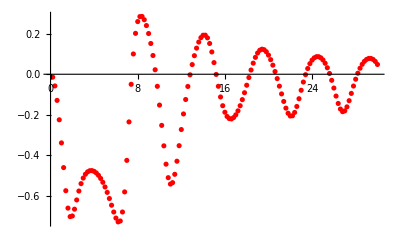

{{0.2,-0.0143262},{0.4,-0.0576804},{0.6,-0.129038},{0.8,-0.224866},{1.,-0.338888},{1.2,-0.460884},{1.4,-0.574958},{1.6,-0.660914},{1.8,-0.702797},{2.,-0.699732},{2.2,-0.666149},{2.4,-0.62067},{2.6,-0.576579},{2.8,-0.540068},{3.,-0.512653},{3.2,-0.493716},{3.4,-0.482013},{3.6,-0.476339},{3.8,-0.475744},{4.,-0.479563},{4.2,-0.487388},{4.4,-0.499012},{4.6,-0.514375},{4.8,-0.533516},{5.,-0.556494},{5.2,-0.583284},{5.4,-0.613596},{5.6,-0.646542},{5.8,-0.680077},{6.,-0.710065},{6.2,-0.728935},{6.4,-0.724438},{6.6,-0.680097},{6.8,-0.580827},{7.,-0.425151},{7.2,-0.235317},{7.4,-0.049613},{7.6,0.100079},{7.8,0.201868},{8.,0.259998},{8.2,0.284579},{8.4,0.285306},{8.6,0.269157},{8.8,0.240369},{9.,0.201063},{9.2,0.151877},{9.4,0.0924893},{9.6,0.0221619},{9.8,-0.0596268},{10.,-0.152218},{10.2,-0.252478},{10.4,-0.353449},{10.6,-0.443962},{10.8,-0.510594},{11.,-0.542254},{11.2,-0.535109},{11.4,-0.493995},{11.6,-0.429393},{11.8,-0.352717},{12.,-0.272976},{12.2,-0.195977},{12.4,-0.124687},{12.6,-0.0602578},{12.8,-0.00286102},{13.,0.0477051},{13.2,0.0916347},{13.4,0.128854},{13.6,0.158863},{13.8,0.180638},{14.,0.192627},{14.2,0.192926},{14.4,0.179689},{14.6,0.151884},{14.8,0.11015},{15.,0.0574989},{15.2,-0.0010533},{15.4,-0.0594205},{15.6,-0.112111},{15.8,-0.15537},{16.,-0.18749},{16.2,-0.208395},{16.4,-0.218956},{16.6,-0.220391},{16.8,-0.213876},{17.,-0.200385},{17.2,-0.180687},{17.4,-0.155426},{17.6,-0.125278},{17.8,-0.0911289},{18.,-0.054212},{18.2,-0.016198},{18.4,0.0208548},{18.6,0.0547177},{18.8,0.0832634},{19.,0.104836},{19.2,0.118467},{19.4,0.123741},{19.6,0.12103},{19.8,0.110946},{20.,0.0943421},{20.2,0.0720347},{20.4,0.0447909},{20.6,0.0133637},{20.8,-0.0214985},{21.,-0.0586928},{21.2,-0.0970627},{21.4,-0.134227},{21.6,-0.167312},{21.8,-0.192568},{22.,-0.206098},{22.2,-0.204994},{22.4,-0.188589},{22.6,-0.159059},{22.8,-0.120842},{23.,-0.0791544},{23.2,-0.0385583},{23.4,-0.00219662},{23.6,0.0282545},{23.8,0.0521953},{24.,0.0696763},{24.2,0.0810048},{24.4,0.0865625},{24.6,0.0866229},{24.8,0.0813018},{25.,0.0705484},{25.2,0.0541815},{25.4,0.031961},{25.6,0.00377798},{25.8,-0.0300157},{26.,-0.0681293},{26.2,-0.107772},{26.4,-0.144278},{26.6,-0.171764},{26.8,-0.184793},{27.,-0.180711},{27.2,-0.161018},{27.4,-0.13048},{27.6,-0.0945901},{27.8,-0.0582034},{28.,-0.0244399},{28.2,0.00504755},{28.4,0.0296072},{28.6,0.0490603},{28.8,0.0635367},{29.,0.0731551},{29.2,0.0779746},{29.4,0.0780057},{29.6,0.073123},{29.8,0.0632046},{30.,0.0482635}}

```mathematica
Getv2kT[1.2]
```

For b = 1.3 Computation time: 852.984324

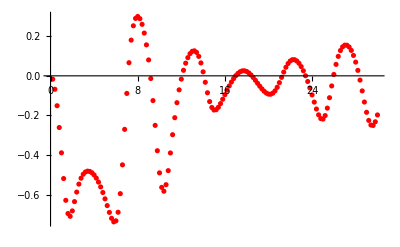

{{0.2,-0.0168808},{0.4,-0.0678336},{0.6,-0.151045},{0.8,-0.261192},{1.,-0.388895},{1.2,-0.518853},{1.4,-0.628789},{1.6,-0.695593},{1.8,-0.709628},{2.,-0.682224},{2.2,-0.635404},{2.4,-0.587274},{2.6,-0.546989},{2.8,-0.517139},{3.,-0.497217},{3.2,-0.485781},{3.4,-0.481397},{3.6,-0.482941},{3.8,-0.489638},{4.,-0.501009},{4.2,-0.516794},{4.4,-0.536871},{4.6,-0.561155},{4.8,-0.589465},{5.,-0.621317},{5.2,-0.655573},{5.4,-0.689887},{5.6,-0.719847},{5.8,-0.737891},{6.,-0.732491},{6.2,-0.689111},{6.4,-0.595213},{6.6,-0.449739},{6.8,-0.270452},{7.,-0.088783},{7.2,0.0662929},{7.4,0.180342},{7.6,0.252726},{7.8,0.290007},{8.,0.299942},{8.2,0.288708},{8.4,0.260172},{8.6,0.21607},{8.8,0.156469},{9.,0.0803333},{9.2,-0.0135633},{9.4,-0.1251},{9.6,-0.2503},{9.8,-0.378293},{10.,-0.490159},{10.2,-0.563496},{10.4,-0.583128},{10.6,-0.549937},{10.8,-0.478983},{11.,-0.389656},{11.2,-0.297441},{11.4,-0.211444},{11.6,-0.135627},{11.8,-0.0708845},{12.,-0.0166887},{12.2,0.0279425},{12.4,0.0639295},{12.6,0.0918762},{12.8,0.111934},{13.,0.123726},{13.2,0.126328},{13.4,0.118342},{13.6,0.0982602},{13.8,0.0651971},{14.,0.0201782},{14.2,-0.0325331},{14.4,-0.0855273},{14.6,-0.130057},{14.8,-0.159762},{15.,-0.172742},{15.2,-0.171117},{15.4,-0.158921},{15.6,-0.140227},{15.8,-0.11825},{16.,-0.0951978},{16.2,-0.0724858},{16.4,-0.0510003},{16.6,-0.0313232},{16.8,-0.0139031},{17.,0.000848015},{17.2,0.0125241},{17.4,0.020715},{17.6,0.0251098},{17.8,0.0255322},{18.,0.0219357},{18.2,0.0146776},{18.4,0.00432324},{18.6,-0.00840425},{18.8,-0.0226604},{19.,-0.0375636},{19.2,-0.052274},{19.4,-0.0659836},{19.6,-0.0778435},{19.8,-0.0869739},{20.,-0.0922346},{20.2,-0.0928554},{20.4,-0.0875791},{20.6,-0.0758716},{20.8,-0.0577711},{21.,-0.0343906},{21.2,-0.00780584},{21.4,0.0190124},{21.6,0.0431685},{21.8,0.0624013},{22.,0.0753355},{22.2,0.0815519},{22.4,0.0812586},{22.6,0.0749718},{22.8,0.063281},{23.,0.0467031},{23.2,0.0256517},{23.4,0.000430753},{23.6,-0.0286437},{23.8,-0.0611943},{24.,-0.0963564},{24.2,-0.132669},{24.4,-0.167556},{24.6,-0.197066},{24.8,-0.215904},{25.,-0.218443},{25.2,-0.200805},{25.4,-0.163182},{25.6,-0.110554},{25.8,-0.0510798},{26.,0.007013},{26.2,0.0578091},{26.4,0.0983096},{26.6,0.127672},{26.8,0.146282},{27.,0.155011},{27.2,0.154625},{27.4,0.145687},{27.6,0.128465},{27.8,0.103007},{28.,0.0693227},{28.2,0.0275298},{28.4,-0.0216435},{28.6,-0.0761803},{28.8,-0.132335},{29.,-0.184328},{29.2,-0.225231},{29.4,-0.248527},{29.6,-0.250629},{29.8,-0.232204},{30.,-0.197641}}

```mathematica
Getv2kT[1.3]
```

For b = 1.4 Computation time: 792.696236

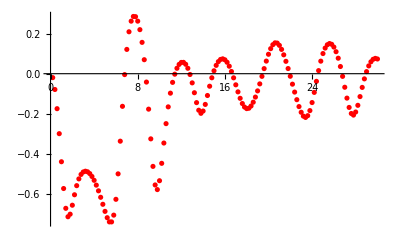

{{0.2,-0.0196333},{0.4,-0.078721},{0.6,-0.174383},{0.8,-0.298934},{1.,-0.438858},{1.2,-0.572404},{1.4,-0.671063},{1.6,-0.713053},{1.8,-0.700298},{2.,-0.655632},{2.2,-0.603493},{2.4,-0.558122},{2.6,-0.524347},{2.8,-0.502165},{3.,-0.489976},{3.2,-0.486058},{3.4,-0.489041},{3.6,-0.497977},{3.8,-0.512259},{4.,-0.531519},{4.2,-0.555498},{4.4,-0.583888},{4.6,-0.616118},{4.8,-0.651019},{5.,-0.686309},{5.2,-0.717851},{5.4,-0.738757},{5.6,-0.738775},{5.8,-0.705072},{6.,-0.62617},{6.2,-0.499223},{6.4,-0.336379},{6.6,-0.162648},{6.8,-0.00448032},{7.,0.121101},{7.2,0.208992},{7.4,0.261911},{7.6,0.285334},{7.8,0.284289},{8.,0.261999},{8.2,0.21957},{8.4,0.156189},{8.6,0.0697316},{8.8,-0.0417326},{9.,-0.176707},{9.2,-0.324832},{9.4,-0.462033},{9.6,-0.554584},{9.8,-0.577698},{10.,-0.533496},{10.2,-0.44677},{10.4,-0.345641},{10.6,-0.248964},{10.8,-0.165356},{11.,-0.0970294},{11.2,-0.0432602},{11.4,-0.00242575},{11.6,0.0270606},{11.8,0.0463717},{12.,0.0561494},{12.2,0.0564971},{12.4,0.0470277},{12.6,0.0270441},{12.8,-0.00402511},{13.,-0.0456944},{13.2,-0.0948729},{13.4,-0.144188},{13.6,-0.182107},{13.8,-0.197529},{14.,-0.186143},{14.2,-0.153109},{14.4,-0.108692},{14.6,-0.0624108},{14.8,-0.0203336},{15.,0.0146363},{15.2,0.0415423},{15.4,0.06029},{15.6,0.071066},{15.8,0.0740431},{16.,0.0693126},{16.2,0.0569817},{16.4,0.0373231},{16.6,0.0110054},{16.8,-0.0206339},{17.,-0.0554732},{17.2,-0.090575},{17.4,-0.122696},{17.6,-0.148685},{17.8,-0.16621},{18.,-0.174043},{18.2,-0.172075},{18.4,-0.161025},{18.6,-0.142084},{18.8,-0.116563},{19.,-0.0857304},{19.2,-0.050806},{19.4,-0.013244},{19.6,0.0253164},{19.8,0.0628322},{20.,0.096873},{20.2,0.124858},{20.4,0.144378},{20.6,0.153795},{20.8,0.152588},{21.,0.141252},{21.2,0.121149},{21.4,0.0940384},{21.6,0.0616766},{21.8,0.02566},{22.,-0.0127093},{22.2,-0.0522064},{22.4,-0.0916387},{22.6,-0.129529},{22.8,-0.163942},{23.,-0.192317},{23.2,-0.211474},{23.4,-0.218041},{23.6,-0.209221},{23.8,-0.18395},{24.,-0.143852},{24.2,-0.0932182},{24.4,-0.0381441},{24.6,0.0153589},{24.8,0.0625251},{25.,0.100431},{25.2,0.127755},{25.4,0.144302},{25.6,0.150359},{25.8,0.146445},{26.,0.132786},{26.2,0.109667},{26.4,0.0772061},{26.6,0.0358055},{26.8,-0.013328},{27.,-0.0675119},{27.2,-0.121722},{27.4,-0.168198},{27.6,-0.198417},{27.8,-0.206327},{28.,-0.191048},{28.2,-0.157612},{28.4,-0.114153},{28.6,-0.068353},{28.8,-0.0258026},{29.,0.0103372},{29.2,0.0388979},{29.4,0.0592452},{29.6,0.0716456},{29.8,0.0762937},{30.,0.0733151}}

```mathematica
Getv2kT[1.4]
```

For b = 1.5 Computation time: 768.028197

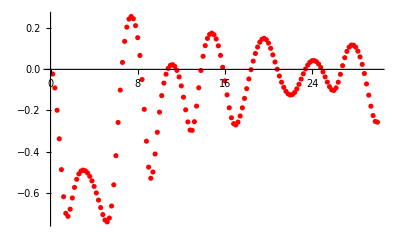

{{0.2,-0.0225849},{0.4,-0.0903293},{0.6,-0.198955},{0.8,-0.33773},{1.,-0.487772},{1.2,-0.619706},{1.4,-0.700477},{1.6,-0.715238},{1.8,-0.68027},{2.,-0.625911},{2.2,-0.574384},{2.4,-0.53491},{2.6,-0.508836},{2.8,-0.494585},{3.,-0.490097},{3.2,-0.493669},{3.4,-0.504092},{3.6,-0.520572},{3.8,-0.542577},{4.,-0.569645},{4.2,-0.601174},{4.4,-0.636097},{4.6,-0.672432},{4.8,-0.706641},{5.,-0.732837},{5.2,-0.742201},{5.4,-0.723303},{5.6,-0.664949},{5.8,-0.561689},{6.,-0.419878},{6.2,-0.258302},{6.4,-0.100768},{6.6,0.0338352},{6.8,0.13629},{7.,0.205554},{7.2,0.244698},{7.4,0.257531},{7.6,0.246678},{7.8,0.212762},{8.,0.154221},{8.2,0.0678223},{8.4,-0.0493131},{8.6,-0.194349},{8.8,-0.349407},{9.,-0.475717},{9.2,-0.529884},{9.4,-0.499362},{9.6,-0.411802},{9.8,-0.306114},{10.,-0.208009},{10.2,-0.127747},{10.4,-0.0668272},{10.6,-0.0234449},{10.8,0.00479334},{11.,0.0198515},{11.2,0.0229733},{11.4,0.0146979},{11.6,-0.00504469},{11.8,-0.0366672},{12.,-0.0804098},{12.2,-0.135253},{12.4,-0.196977},{12.6,-0.255646},{12.8,-0.294827},{13.,-0.296806},{13.2,-0.254546},{13.4,-0.178543},{13.6,-0.0895514},{13.8,-0.00560935},{14.,0.0636903},{14.2,0.115587},{14.4,0.150663},{14.6,0.170439},{14.8,0.176213},{15.,0.168717},{15.2,0.14817},{15.4,0.114547},{15.6,0.0681306},{15.8,0.0102922},{16.,-0.0556897},{16.2,-0.124005},{16.4,-0.186722},{16.6,-0.235492},{16.8,-0.264119},{17.,-0.270461},{17.2,-0.256525},{17.4,-0.226924},{17.6,-0.18698},{17.8,-0.141423},{18.,-0.0938029},{18.2,-0.0465261},{18.4,-0.00138467},{18.6,0.0403393},{18.8,0.0774649},{19.,0.108579},{19.2,0.132224},{19.4,0.14685},{19.6,0.151211},{19.8,0.144697},{20.,0.127848},{20.2,0.102358},{20.4,0.0707718},{20.6,0.0360407},{20.8,0.000842436},{21.,-0.0324741},{21.2,-0.0623243},{21.4,-0.0874052},{21.6,-0.106713},{21.8,-0.11941},{22.,-0.12473},{22.2,-0.122278},{22.4,-0.112087},{22.6,-0.0949594},{22.8,-0.0725072},{23.,-0.0471723},{23.2,-0.0215148},{23.4,0.00191063},{23.6,0.0211369},{23.8,0.0346975},{24.,0.0420257},{24.2,0.0428884},{24.4,0.0374463},{24.6,0.0259866},{24.8,0.00916929},{25.,-0.0121979},{25.2,-0.0365276},{25.4,-0.0617366},{25.6,-0.0841236},{25.8,-0.0993642},{26.,-0.102544},{26.2,-0.0901839},{26.4,-0.0624577},{26.6,-0.0239669},{26.8,0.0180939},{27.,0.0568571},{27.2,0.0875611},{27.4,0.108198},{27.6,0.118095},{27.8,0.117883},{28.,0.107848},{28.2,0.0886622},{28.4,0.060718},{28.6,0.024347},{28.8,-0.0198833},{29.,-0.0706694},{29.2,-0.125358},{29.4,-0.179143},{29.6,-0.224716},{29.8,-0.253236},{30.,-0.256957}}

```mathematica
Getv2kT[1.5]
```

For b = 1.6 Computation time: 807.011375

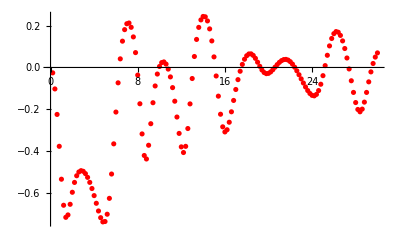

{{0.2,-0.0257343},{0.4,-0.102642},{0.6,-0.224655},{0.8,-0.377174},{1.,-0.534568},{1.2,-0.659201},{1.4,-0.71694},{1.6,-0.70542},{1.8,-0.654608},{2.,-0.597057},{2.2,-0.550005},{2.4,-0.518006},{2.6,-0.500013},{2.8,-0.493652},{3.,-0.496776},{3.2,-0.50782},{3.4,-0.525725},{3.6,-0.549731},{3.8,-0.579141},{4.,-0.613012},{4.2,-0.649749},{4.4,-0.686545},{4.6,-0.718671},{4.8,-0.738806},{5.,-0.736975},{5.2,-0.702084},{5.4,-0.626138},{5.6,-0.509795},{5.8,-0.365395},{6.,-0.213306},{6.2,-0.0734355},{6.4,0.0412483},{6.6,0.125888},{6.8,0.181006},{7.,0.209186},{7.2,0.2127},{7.4,0.192215},{7.6,0.146201},{7.8,0.071125},{8.,-0.0365048},{8.2,-0.173611},{8.4,-0.317883},{8.6,-0.421089},{8.8,-0.437797},{9.,-0.372126},{9.2,-0.269073},{9.4,-0.168645},{9.6,-0.0884451},{9.8,-0.0314517},{10.,0.00472272},{10.2,0.0232477},{10.4,0.0265625},{10.6,0.0160713},{10.8,-0.00775585},{11.,-0.0451136},{11.2,-0.0964101},{11.4,-0.161336},{11.6,-0.237078},{11.8,-0.315424},{12.,-0.379853},{12.2,-0.406924},{12.4,-0.377378},{12.6,-0.292116},{12.8,-0.174246},{13.,-0.0528428},{13.2,0.0525126},{13.4,0.134178},{13.6,0.191808},{13.8,0.227663},{14.,0.244068},{14.2,0.242366},{14.4,0.222782},{14.6,0.184579},{14.8,0.127036},{15.,0.0506037},{15.2,-0.0406977},{15.4,-0.137206},{15.6,-0.22369},{15.8,-0.283967},{16.,-0.308355},{16.2,-0.297934},{16.4,-0.261971},{16.6,-0.212055},{16.8,-0.157748},{17.,-0.105331},{17.2,-0.0582129},{17.4,-0.0179989},{17.6,0.0146255},{17.8,0.0393823},{18.,0.0560954},{18.2,0.0646449},{18.4,0.0650511},{18.6,0.0576929},{18.8,0.0437084},{19.,0.0252591},{19.2,0.00552619},{19.4,-0.0119387},{19.6,-0.0241244},{19.8,-0.029478},{20.,-0.0280767},{20.2,-0.0211968},{20.4,-0.0106968},{20.6,0.0014438},{20.8,0.013642},{21.,0.0244521},{21.2,0.0327518},{21.4,0.0376825},{21.6,0.0386351},{21.8,0.0353222},{22.,0.0276789},{22.2,0.0161685},{22.4,0.00138848},{22.6,-0.0158632},{22.8,-0.0347704},{23.,-0.0545013},{23.2,-0.0742569},{23.4,-0.0931864},{23.6,-0.110384},{23.8,-0.124287},{24.,-0.133432},{24.2,-0.135735},{24.4,-0.128735},{24.6,-0.11052},{24.8,-0.0802138},{25.,-0.0392158},{25.2,0.00885008},{25.4,0.0583327},{25.6,0.103194},{25.8,0.138652},{26.,0.161736},{26.2,0.171682},{26.4,0.168582},{26.6,0.153446},{26.8,0.12709},{27.,0.0906878},{27.2,0.0453862},{27.4,-0.00704808},{27.6,-0.0635832},{27.8,-0.119414},{28.,-0.167808},{28.2,-0.200847},{28.4,-0.212062},{28.6,-0.199211},{28.8,-0.165757},{29.,-0.119389},{29.2,-0.068813},{29.4,-0.0211408},{29.6,0.0190897},{29.8,0.0496683},{30.,0.0697212}}

```mathematica
Getv2kT[1.6]
```

For b = 1.7 Computation time: 745.547209

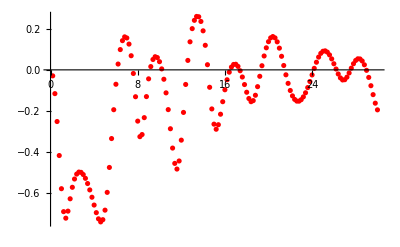

{{0.2,-0.0290825},{0.4,-0.115642},{0.6,-0.251364},{0.8,-0.416816},{1.,-0.578162},{1.2,-0.689792},{1.4,-0.721522},{1.6,-0.687351},{1.8,-0.627272},{2.,-0.571362},{2.2,-0.531033},{2.4,-0.507147},{2.6,-0.497241},{2.8,-0.498637},{3.,-0.509284},{3.2,-0.527755},{3.4,-0.553014},{3.6,-0.584091},{3.8,-0.619706},{4.,-0.657761},{4.2,-0.694704},{4.4,-0.724805},{4.6,-0.739694},{4.8,-0.728926},{5.,-0.682561},{5.2,-0.596049},{5.4,-0.47478},{5.6,-0.334199},{5.8,-0.193879},{6.,-0.070044},{6.2,0.0283226},{6.4,0.0986808},{6.6,0.142091},{6.8,0.160541},{7.,0.155182},{7.2,0.125419},{7.4,0.068773},{7.6,-0.0175507},{7.8,-0.130743},{8.,-0.249359},{8.2,-0.32504},{8.4,-0.314728},{8.6,-0.232493},{8.8,-0.130072},{9.,-0.0436847},{9.2,0.0160014},{9.4,0.0504919},{9.6,0.0639534},{9.8,0.0597495},{10.,0.0398024},{10.2,0.00475306},{10.4,-0.0456544},{10.6,-0.111882},{10.8,-0.193422},{11.,-0.286486},{11.2,-0.380498},{11.4,-0.455002},{11.6,-0.482583},{11.8,-0.443296},{12.,-0.341952},{12.2,-0.207082},{12.4,-0.0709768},{12.6,0.0459885},{12.8,0.136485},{13.,0.200629},{13.2,0.240985},{13.4,0.259838},{13.6,0.258269},{13.8,0.235554},{14.,0.189931},{14.2,0.119499},{14.4,0.0251182},{14.6,-0.0847204},{14.8,-0.19007},{15.,-0.264114},{15.2,-0.288831},{15.4,-0.26681},{15.6,-0.215787},{15.8,-0.154849},{16.,-0.0968429},{16.2,-0.048154},{16.4,-0.0111998},{16.6,0.0135572},{16.8,0.0263061},{17.,0.0273003},{17.2,0.0169166},{17.4,-0.00428366},{17.6,-0.0347706},{17.8,-0.0714716},{18.,-0.108912},{18.2,-0.139414},{18.4,-0.154802},{18.6,-0.149596},{18.8,-0.123595},{19.,-0.0816827},{19.2,-0.0313576},{19.4,0.020162},{19.6,0.0675267},{19.8,0.10727},{20.,0.137124},{20.2,0.155725},{20.4,0.16207},{20.6,0.1556},{20.8,0.136404},{21.,0.105671},{21.2,0.0659914},{21.4,0.0212467},{21.6,-0.0240438},{21.8,-0.0656492},{22.,-0.100365},{22.2,-0.126495},{22.4,-0.143561},{22.6,-0.151968},{22.8,-0.152185},{23.,-0.145123},{23.2,-0.13136},{23.4,-0.111453},{23.6,-0.0861862},{23.8,-0.0566628},{24.,-0.0247003},{24.2,0.00736246},{24.4,0.0371392},{24.6,0.0620951},{24.8,0.080284},{25.,0.0905314},{25.2,0.0925159},{25.4,0.0862801},{25.6,0.0729043},{25.8,0.0534662},{26.,0.0297434},{26.2,0.00420767},{26.4,-0.0200742},{26.6,-0.039028},{26.8,-0.0491134},{27.,-0.0478393},{27.2,-0.0354533},{27.4,-0.0151099},{27.6,0.00831451},{27.8,0.0298549},{28.,0.0457442},{28.2,0.053781},{28.4,0.0530138},{28.6,0.0432305},{28.8,0.0246256},{29.,-0.00233426},{29.2,-0.0367736},{29.4,-0.0770723},{29.6,-0.120519},{29.8,-0.162068},{30.,-0.194564}}

```mathematica
Getv2kT[1.7]
```

For b = 1.8 Computation time: 817.002039

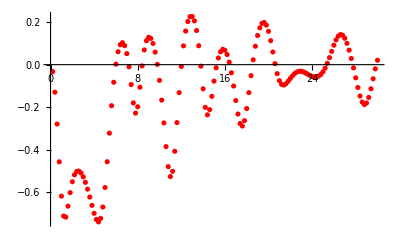

{{0.2,-0.0326288},{0.4,-0.129307},{0.6,-0.27895},{0.8,-0.456167},{1.,-0.617519},{1.2,-0.710979},{1.4,-0.716163},{1.6,-0.664567},{1.8,-0.600969},{2.,-0.549939},{2.2,-0.517456},{2.4,-0.50183},{2.6,-0.499869},{2.8,-0.508878},{3.,-0.526937},{3.2,-0.552652},{3.4,-0.584761},{3.6,-0.621668},{3.8,-0.66085},{4.,-0.698147},{4.2,-0.727052},{4.4,-0.73848},{4.6,-0.721893},{4.8,-0.668662},{5.,-0.577123},{5.2,-0.455882},{5.4,-0.321664},{5.6,-0.192781},{5.8,-0.0826095},{6.,0.00231687},{6.2,0.0606967},{6.4,0.0937662},{6.6,0.103107},{6.8,0.0893705},{7.,0.0519269},{7.2,-0.0100789},{7.4,-0.0932885},{7.6,-0.179628},{7.8,-0.227502},{8.,-0.197798},{8.2,-0.10609},{8.4,-0.00579941},{8.6,0.0691239},{8.8,0.112432},{9.,0.1287},{9.2,0.123271},{9.4,0.0995406},{9.6,0.0589122},{9.8,0.00134739},{10.,-0.0738194},{10.2,-0.166555},{10.4,-0.273668},{10.6,-0.384866},{10.8,-0.478875},{11.,-0.525555},{11.2,-0.500895},{11.4,-0.406769},{11.6,-0.272015},{11.8,-0.131543},{12.,-0.00846405},{12.2,0.0881962},{12.4,0.15781},{12.6,0.202702},{12.8,0.225277},{13.,0.226418},{13.2,0.205512},{13.4,0.160391},{13.6,0.0888828},{13.8,-0.006965},{14.,-0.113423},{14.2,-0.200542},{14.4,-0.235673},{14.6,-0.211072},{14.8,-0.148731},{15.,-0.0772741},{15.2,-0.0147982},{15.4,0.031518},{15.6,0.0602743},{15.8,0.0720447},{16.,0.0676226},{16.2,0.047492},{16.4,0.0119494},{16.6,-0.0381818},{16.8,-0.100327},{17.,-0.16848},{17.2,-0.23193},{17.4,-0.276241},{17.6,-0.28824},{17.8,-0.2629},{18.,-0.206215},{18.2,-0.131279},{18.4,-0.0516832},{18.6,0.0227987},{18.8,0.0865434},{19.,0.137025},{19.2,0.17292},{19.4,0.193508},{19.6,0.197987},{19.8,0.185601},{20.,0.156415},{20.2,0.1126},{20.4,0.0593251},{20.6,0.00473515},{20.8,-0.0422323},{21.,-0.0752223},{21.2,-0.0923779},{21.4,-0.0957736},{21.6,-0.0896297},{21.8,-0.0781744},{22.,-0.0648983},{22.2,-0.052345},{22.4,-0.0420046},{22.6,-0.0349209},{22.8,-0.031305},{23.,-0.0311143},{23.2,-0.0339293},{23.4,-0.0388087},{23.6,-0.0447197},{23.8,-0.0505382},{24.,-0.0551528},{24.2,-0.057652},{24.4,-0.0575094},{24.6,-0.053824},{24.8,-0.0461049},{25.,-0.0337648},{25.2,-0.0163315},{25.4,0.00619007},{25.6,0.0330937},{25.8,0.0625041},{26.,0.0914647},{26.2,0.11641},{26.4,0.133795},{26.6,0.141389},{26.8,0.13803},{27.,0.12402},{27.2,0.100257},{27.4,0.0680681},{27.6,0.0289997},{27.8,-0.0151781},{28.,-0.0617076},{28.2,-0.107238},{28.4,-0.147068},{28.6,-0.175649},{28.8,-0.187709},{29.,-0.180175},{29.2,-0.153784},{29.4,-0.113379},{29.6,-0.0662672},{29.8,-0.0196937},{30.,0.0206598}}

```mathematica
Getv2kT[1.8]
```

For b = 1.9 Computation time: 773.1428

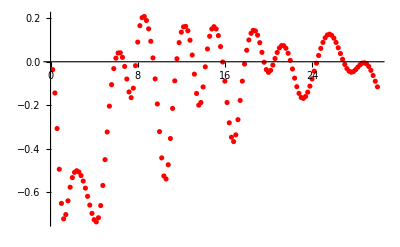

{{0.2,-0.0363724},{0.4,-0.143615},{0.6,-0.307266},{0.8,-0.494706},{1.,-0.651729},{1.2,-0.722908},{1.4,-0.70326},{1.6,-0.639961},{1.8,-0.577328},{2.,-0.533134},{2.2,-0.50895},{2.4,-0.501494},{2.6,-0.507298},{2.8,-0.523765},{3.,-0.549028},{3.2,-0.5815},{3.4,-0.619301},{3.6,-0.659583},{3.8,-0.697743},{4.,-0.726717},{4.2,-0.736916},{4.4,-0.717798},{4.6,-0.661741},{4.8,-0.569097},{5.,-0.45045},{5.2,-0.323131},{5.4,-0.204258},{5.6,-0.105374},{5.8,-0.0315664},{6.,0.0165408},{6.2,0.0402835},{6.4,0.0411783},{6.6,0.020223},{6.8,-0.0214573},{7.,-0.0795246},{7.2,-0.13881},{7.4,-0.165163},{7.6,-0.121624},{7.8,-0.0180236},{8.,0.0906447},{8.2,0.166068},{8.4,0.202871},{8.6,0.208445},{8.8,0.18997},{9.,0.151475},{9.2,0.0942151},{9.4,0.0177209},{9.6,-0.0788201},{9.8,-0.194276},{10.,-0.321546},{10.2,-0.442327},{10.4,-0.525587},{10.6,-0.539293},{10.8,-0.47403},{11.,-0.353169},{11.2,-0.214724},{11.4,-0.0878662},{11.6,0.0139627},{11.8,0.0880554},{12.,0.136122},{12.2,0.160644},{12.4,0.162883},{12.6,0.14283},{12.8,0.0991321},{13.,0.0309821},{13.2,-0.0569439},{13.4,-0.145957},{13.6,-0.199921},{13.8,-0.187434},{14.,-0.115937},{14.2,-0.0232144},{14.4,0.0588907},{14.6,0.117416},{14.8,0.150898},{15.,0.161451},{15.2,0.150969},{15.4,0.120322},{15.6,0.0695914},{15.8,-0.00109327},{16.,-0.0893106},{16.2,-0.18766},{16.4,-0.280892},{16.6,-0.347257},{16.8,-0.367399},{17.,-0.33633},{17.2,-0.266368},{17.4,-0.178032},{17.6,-0.089128},{17.8,-0.0104571},{18.,0.0531088},{18.2,0.100256},{18.4,0.130738},{18.6,0.144564},{18.8,0.14175},{19.,0.122357},{19.2,0.0878985},{19.4,0.0432726},{19.6,-0.00216626},{19.8,-0.0360152},{20.,-0.0488329},{20.2,-0.0396245},{20.4,-0.0152243},{20.6,0.014847},{20.8,0.0427198},{21.,0.0634779},{21.2,0.0743172},{21.4,0.0739665},{21.6,0.0621224},{21.8,0.0390557},{22.,0.00636031},{22.2,-0.0333075},{22.4,-0.075458},{22.6,-0.11469},{22.8,-0.145589},{23.,-0.164137},{23.2,-0.168639},{23.4,-0.159769},{23.6,-0.13999},{23.8,-0.112165},{24.,-0.0791339},{24.2,-0.0432465},{24.4,-0.00673923},{24.6,0.0287657},{24.8,0.0613557},{25.,0.0891294},{25.2,0.110236},{25.4,0.123158},{25.6,0.126962},{25.8,0.12178},{26.,0.108523},{26.2,0.0889137},{26.4,0.0641389},{26.6,0.0377726},{26.8,0.0115079},{27.,-0.0123054},{27.2,-0.0313718},{27.4,-0.0435346},{27.6,-0.0480653},{27.8,-0.0449829},{28.,-0.0361992},{28.2,-0.0247385},{28.4,-0.0138883},{28.6,-0.00655493},{28.8,-0.00475199},{29.,-0.00962716},{29.2,-0.0214223},{29.4,-0.0396886},{29.6,-0.0632153},{29.8,-0.0897282},{30.,-0.115606}}

```mathematica
Getv2kT[1.9]
```

For b = 2. Computation time: 714.854377

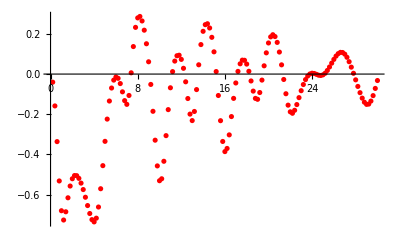

{{0.2,-0.0403132},{0.4,-0.158541},{0.6,-0.336156},{0.8,-0.531889},{1.,-0.680079},{1.2,-0.726317},{1.4,-0.685273},{1.6,-0.615663},{1.8,-0.557188},{2.,-0.520875},{2.2,-0.505072},{2.4,-0.505605},{2.6,-0.518984},{2.8,-0.542693},{3.,-0.574735},{3.2,-0.612968},{3.4,-0.65432},{3.6,-0.693925},{3.8,-0.724358},{4.,-0.735652},{4.2,-0.717132},{4.4,-0.661622},{4.6,-0.570603},{4.8,-0.455768},{5.,-0.334779},{5.2,-0.224086},{5.4,-0.134215},{5.6,-0.0694702},{5.8,-0.0300941},{6.,-0.0145918},{6.2,-0.0210763},{6.4,-0.0472591},{6.6,-0.0884375},{6.8,-0.132158},{7.,-0.15066},{7.2,-0.106485},{7.4,0.00633025},{7.6,0.136892},{7.8,0.232423},{8.,0.279479},{8.2,0.286683},{8.4,0.264321},{8.6,0.218388},{8.8,0.150836},{9.,0.0611568},{9.2,-0.0515872},{9.4,-0.18528},{9.6,-0.329051},{9.8,-0.457011},{10.,-0.530749},{10.2,-0.521075},{10.4,-0.433991},{10.6,-0.306362},{10.8,-0.176939},{11.,-0.0682472},{11.2,0.0122348},{11.4,0.0646102},{11.6,0.0912108},{11.8,0.0937741},{12.,0.0730315},{12.2,0.0286679},{12.4,-0.0385323},{12.6,-0.121718},{12.8,-0.199227},{13.,-0.231491},{13.2,-0.186098},{13.4,-0.0772089},{13.6,0.0461514},{13.8,0.146717},{14.,0.212727},{14.2,0.24585},{14.4,0.250433},{14.6,0.229265},{14.8,0.182869},{15.,0.110689},{15.2,0.0125604},{15.4,-0.106666},{15.6,-0.231982},{15.8,-0.33538},{16.,-0.385842},{16.2,-0.370151},{16.4,-0.302585},{16.6,-0.21152},{16.8,-0.120996},{17.,-0.0443391},{17.2,0.0133332},{17.4,0.0510814},{17.6,0.0693256},{17.8,0.0686069},{18.,0.0496671},{18.2,0.0138659},{18.4,-0.034296},{18.6,-0.0848177},{18.8,-0.121059},{19.,-0.125585},{19.2,-0.0918597},{19.4,-0.0300176},{19.6,0.0410897},{19.8,0.105621},{20.,0.154777},{20.2,0.185146},{20.4,0.195784},{20.6,0.186625},{20.8,0.157585},{21.,0.10959},{21.2,0.0458898},{21.4,-0.0268836},{21.6,-0.0978916},{21.8,-0.154704},{22.,-0.187853},{22.2,-0.195061},{22.4,-0.180193},{22.6,-0.15179},{22.8,-0.117304},{23.,-0.082763},{23.2,-0.0520801},{23.4,-0.0274293},{23.6,-0.00989747},{23.8,0.000448161},{24.,0.00420776},{24.2,0.00284682},{24.4,-0.00133791},{24.6,-0.00556321},{24.8,-0.00708026},{25.,-0.00381861},{25.2,0.00412961},{25.4,0.017866},{25.6,0.0352367},{25.8,0.0542923},{26.,0.0730329},{26.2,0.0894268},{26.4,0.101627},{26.6,0.107988},{26.8,0.107336},{27.,0.0991263},{27.2,0.0835648},{27.4,0.0615382},{27.6,0.0344656},{27.8,0.00383808},{28.,-0.0287152},{28.2,-0.0614795},{28.4,-0.0926121},{28.6,-0.119729},{28.8,-0.14009},{29.,-0.150781},{29.2,-0.149264},{29.4,-0.13442},{29.6,-0.107213},{29.8,-0.0714302},{30.,-0.0321124}}

```mathematica
Getv2kT[2.0]
```